## Initialization

```mathematica
(*get association of resources,name of local host and remove local host from available resources*)hosts=Counts[ReadList[Environment["NODEFILE"],"String"]]
local=First[StringSplit[Environment["HOSTNAME"],"."]]
hosts[local]--;
(*launch subkernels and connect them to the controlling Wolfram Kernel*)
Needs["SubKernels`RemoteKernels`"];
Map[If[hosts[#]>0,LaunchKernels[RemoteMachine[#,"ssh -x -f -l `3` `1` /gpfs/runtime/opt/mathematica/12.0/Executables/wolfram -wstp -linkmode Connect `4` -linkname '`2`' -subkernel -noinit",hosts[#]]]]&,Keys[hosts]];
dir=DirectoryName[$InputFileName];
```

```mathematica
dir=NotebookDirectory[];
SetDirectory[NotebookDirectory[]];
(*MeshDir = "../mesh";*)
ResultDir = "Result1";
ParallelEvaluate[$HistoryLength=0];
$HistoryLength=0;
<<NDSolve`FEM`
```

## Problem Solution: Numerics

### Numerics subroutine:

```mathematica
ApplyBC[𝓉0_]:=Module[{𝓉 = 𝓉0,uhat,vhat,what,x,𝓉x,𝓉y,𝓉z,normals},
uhat[x_List]:=-((-7+8 ν[x]) Cos[γ-(ArcTan@@x)/2]+2 Cos[γ+(ArcTan@@x)/2]+Cos[γ+(3 ArcTan@@x)/2])/(4 √(2 π))Knorm Sqrt[R0]/μ[x] 𝓉;
vhat[x_List]:=1/(2 √(2 π))((-3+4 ν[x]) Sin[γ-(ArcTan@@x)/2]+Sin[γ+(ArcTan@@x)/2]-Cos[γ+(ArcTan@@x)/2] Sin[ArcTan@@x])Knorm Sqrt[R0]/μ[x] 𝓉;
what[x_List]:=0.0;
SetUpDirichletBC[{uhat,vhat,what}];
𝓉x[x_List]:=0.0;
𝓉y[x_List]:=0.0;
𝓉z[x_List]:=0.0;
SetUpNeumannBC[{𝓉x,𝓉y,𝓉z}];
(*normals=Omegasuph["BoundaryNormals"][[1]];
Edges =Extract[Omegasuph["BoundaryElements"][[1,1]],Position[Map[Norm@(#-{0,1})&,normals],x_/;x<10^-5]];*)
Remove[𝓉,uhat,vhat,what,x,𝓉x,𝓉y,𝓉z,normals];
];
SetUpDirichletBC[Funcs_List]:=Module[{BCVals,Nodes1,Nodes2,Nodes,Nodes3,Nodes4,NodesZ
,tol=0.2},
Nodes1 =Flatten@Position[Abs[xOverVecsuph[[;;,1]]^2+xOverVecsuph[[;;,2]]^2-R0^2],x_/;x<tol];
Nodes = Join[{1,#}&/@Nodes1,{2,#}&/@Nodes1];
BCVals=Funcs[[#[[1]]]][xOverVecsuph[[#[[2]]]]]&/@Nodes;
DirichletDof = Sort[(Nodes[[;;,2]]-1)*nsubdof+Nodes[[;;,1]]];
DirichletNode=AssociationThread[Nodes->BCVals];
Remove[BCVals,Nodes1,Nodes2,Nodes,Nodes3,Nodes4,NodesZ];
];
SetUpNeumannBC[Funcs_List]:=Module[{BCVals,Nodes1,Nodes2,Nodes,Nodes3,Nodes4
,tol=0.2},
Nodes1 =Flatten@Position[Abs[xOverVecsuph[[;;,1]]^2+xOverVecsuph[[;;,2]]^2-R0^2],x_/;x<tol];
Nodes = Join[{1,#}&/@Nodes1,{2,#}&/@Nodes1];
BCVals=Funcs[[#[[1]]]][xOverVecsuph[[#[[2]]]]]&/@Nodes;
NeumannDof = DirichletDof;
NeumannBC=AssociationThread[Nodes->BCVals];
Remove[BCVals,Nodes1,Nodes2,Nodes,Nodes3,Nodes4];
];
```

```mathematica
DefineGaussAndSFInfo[ElementType_,integrationOrder_,elementOrder_]:=
Module[{},
GuassPointsNatural=ElementIntegrationPoints[ToExpression[ElementType],integrationOrder];
GuassWeights=ElementIntegrationWeights[ToExpression[ElementType],integrationOrder];
nsubguass=GuassWeights//Length;
NMat=ElementShapeFunction[ToExpression[ElementType],elementOrder];
dN= ElementShapeFunctionDerivative[ToExpression[ElementType],elementOrder];
];
GuassIntegrate[coord_List,f0_]:=Module[{f=f0,GuassPointsSpatial},
GuassPointsSpatial=Apply[NMat,GuassPointsNatural,2].coord;
GuassWeights.MapThread[f,{GuassPointsNatural,GuassPointsSpatial}]
];
ApplyTraction[Edge_]:=
Module[{OutEdge,CoordLine,Jacobi,EquivalentTractionVector,Q},
OutEdge=Flatten[Outer[List,{1,2},Edge],1];
CoordLine =xOverVecsuph[[Edge]];
Jacobi =Norm[Subtract@@CoordLine]/2 ;
EquivalentTractionVector=
Jacobi*ReplacePart[Map[NeumannBC,OutEdge],Position[KeyExistsQ[NeumannBC,#]&/@OutEdge,False]->0.0];
Q=Flatten@IDMat[[;;,Edge]];
rMat[[Q]]+=EquivalentTractionVector;
Remove[OutEdge,CoordLine,Jacobi,EquivalentTractionVector,Q];
]
```

```mathematica
Unprotect[HeavisideTheta];
HeavisideTheta[0.]=0.5;
HeavisideTheta[0]=0.5;
Protect[HeavisideTheta];
Ps=(#+Abs[#])/2&;Ng=(#-Abs[#])/2&;
StiffnessPN[Bsupe_,TransPusupe_,Phisupe_,ξ_List,x_List]:=Module[{ε,λa,Vecs,λp,λn,UnitVecs,Plist,SfP,SfN},
ε=((Bsupe[ξ].TransPusupe)+Transpose[(Bsupe[ξ].TransPusupe)])/2;
{λa,Vecs}=Eigensystem[ε];
UnitVecs=Normalize/@Vecs;
λp =Ps/@λa;
λn =Ng/@λa;
Plist= Permutations[Range[nsubdof],{2}];
SfP=λ[x] HeavisideTheta[Tr[ε]]IdentityMatrix[nsubdof]⊗IdentityMatrix[nsubdof]+
2μ[x] Sum[HeavisideTheta[λa[[n]]]UnitVecs[[n]]⊗UnitVecs[[n]]⊗UnitVecs[[n]]⊗UnitVecs[[n]],{n,nsubdof}]
+μ[x] Total[Apply[If[λa[[#1]]==λa[[#2]],HeavisideTheta[λa[[#1]]],(λp[[#1]]-λp[[#2]])/(λa[[#1]]-λa[[#2]])](UnitVecs[[#1]]⊗UnitVecs[[#2]]⊗UnitVecs[[#1]]⊗UnitVecs[[#2]]+UnitVecs[[#1]]⊗UnitVecs[[#2]]⊗UnitVecs[[#2]]⊗UnitVecs[[#1]])&]/@Plist]//Simplify;
SfN=λ[x]  HeavisideTheta[-Tr[ε]] IdentityMatrix[nsubdof]⊗IdentityMatrix[nsubdof]+
2μ[x] Sum[HeavisideTheta[-λa[[n]]]UnitVecs[[n]]⊗UnitVecs[[n]]⊗UnitVecs[[n]]⊗UnitVecs[[n]],{n,nsubdof}]
+μ[x]Total[Apply[If[λa[[#1]]==λa[[#2]],HeavisideTheta[-λa[[#1]]],(λn[[#1]]-λn[[#2]])/(λa[[#1]]-λa[[#2]])](UnitVecs[[#1]]⊗UnitVecs[[#2]]⊗UnitVecs[[#1]]⊗UnitVecs[[#2]]+UnitVecs[[#1]]⊗UnitVecs[[#2]]⊗UnitVecs[[#2]]⊗UnitVecs[[#1]])&]/@Plist]//Simplify;
SfP((1-Phisupe.(NMat@@ξ))^2+𝒦)+SfN
]
StiffnessP[ε_,Phisupe_,ξ_List,x_List]:=Module[{λa,Vecs,λp,λn,UnitVecs,Plist,SfP},
{λa,Vecs}=Eigensystem[ε[ξ]];
UnitVecs=Normalize/@Vecs;
λp =Ps/@λa;
λn =Ng/@λa;
Plist= Permutations[Range[nsubdof],{2}];
SfP=λ[x] HeavisideTheta[Tr[ε[ξ]]]IdentityMatrix[nsubdof]⊗IdentityMatrix[nsubdof]+
2μ[x] Sum[HeavisideTheta[λa[[n]]]UnitVecs[[n]]⊗UnitVecs[[n]]⊗UnitVecs[[n]]⊗UnitVecs[[n]],{n,nsubdof}]
+μ[x] Total[Apply[If[λa[[#1]]==λa[[#2]],HeavisideTheta[λa[[#1]]],(λp[[#1]]-λp[[#2]])/(λa[[#1]]-λa[[#2]])](UnitVecs[[#1]]⊗UnitVecs[[#2]]⊗UnitVecs[[#1]]⊗UnitVecs[[#2]]+UnitVecs[[#1]]⊗UnitVecs[[#2]]⊗UnitVecs[[#2]]⊗UnitVecs[[#1]])&]/@Plist]//Simplify;
SfP
]
```

```mathematica
ComputeStiffnessMatrixU[e0_]:=Module[{e=e0,B,Q,jsupe,Bsupe,ksupe,Phisupe,ℐk,coord,TransPusupe},
B=IEN[[;;,e]];
coord=xOverVecsuph[[B]];
jsupe=Det@((dN@@#).coord)&;
Bsupe=(Inverse[(dN@@#).coord].dN@@#)&;
Q=Flatten@IDMat[[;;,B]];
Phisupe=PhiMat[[B]];
TransPusupe=Transpose[UMat[[;;,B]]];
ksupe=jsupe[#1]Transpose[Bsupe[#1]].StiffnessPN[Bsupe,TransPusupe,Phisupe,#1,#2].Bsupe[#1]&;
ℐk=Flatten[GuassIntegrate[coord,ksupe],{{2,1},{3,4}}];
KMat[[Q,Q]]+=ℐk;
Remove[e,B,Q,jsupe,Bsupe,ksupe,Phisupe,ℐk,coord,TransPusupe];
]
ComputeResidualMatrixU[e0_]:=Module[{e=e0,B,Q,jsupe,Bsupe,Phisupe,fsupe,rsupe,frsupe,ℐr,TransPusupe,coord},
B=IEN[[;;,e]];
coord=xOverVecsuph[[B]];
jsupe=Det@((dN@@#).coord)&;
Bsupe=(Inverse[(dN@@#).coord].dN@@#)&;
Q=Flatten@IDMat[[;;,B]];
TransPusupe=Transpose[UMat[[;;,B]]];
Phisupe=PhiMat[[B]];
fsupe=-jsupe[#1](3 λ[#2]+2 μ[#2]) alphaDeltaT[#2]Bsupe[#1]&;
rsupe=jsupe[#]TensorContract[StiffnessPN[Bsupe,TransPusupe,Phisupe,#1,#2].(Bsupe[#].TransPusupe),{3,4}].Bsupe[#]&;
frsupe=fsupe[#1,#2]-rsupe[#1,#2]&;
ℐr= Flatten@GuassIntegrate[coord,frsupe];
rMat[[Q]]+=ℐr;
Remove[e,B,Q,jsupe,Bsupe,Phisupe,fsupe,rsupe,frsupe,ℐr,TransPusupe,coord];
]
```

```mathematica
ComputeStiffnessMatrixPhi[e0_]:=Module[{e=e0,B,jsupe,Bsupe,ksupe,ℐk,TransPusupe,Phisupe,ℋ,coord},
B=IEN[[;;,e]];
coord=xOverVecsuph[[B]];
jsupe=Det@((dN@@#).coord)&;
Bsupe=(Inverse[(dN@@#).coord].dN@@#)&;
TransPusupe=Transpose[UMat[[;;,B]]];
Phisupe=PhiMat[[B]];
ℋ=TensorContract[TensorContract[StiffnessContra.(Bsupe[#].TransPusupe),{3,4}].(Bsupe[#].TransPusupe),{1,2}]/2&;
ksupe=jsupe[#1](Gsubc[#2] lsub0 Transpose[Bsupe[#1]].Bsupe[#1]+(2ℋ[#1]+Gsubc[#2]/ lsub0+η/τ)(NMat@@#1)⊗(NMat@@#1))&;
ℐk=GuassIntegrate[coord,ksupe];
KMat[[B,B]]+=ℐk;
Remove[e,B,jsupe,Bsupe,ksupe,ℐk,TransPusupe,Phisupe,ℋ,coord];
]
ComputeResidualMatrixPhi[e0_]:=Module[{e=e0,B,jsupe,Bsupe,Phisupe,fsupe,rsupe,frsupe,ℐr,TransPusupe,ℋ,PhiLaste,coord},
B=IEN[[;;,e]];
coord=xOverVecsuph[[B]];
jsupe=Det@((dN@@#).coord)&;
Bsupe=(Inverse[(dN@@#).coord].dN@@#)&;
TransPusupe=Transpose[UMat[[;;,B]]];
Phisupe=PhiMat[[B]];
PhiLaste=PhiMatLastStep[[B]];
ℋ=TensorContract[TensorContract[StiffnessContra.(Bsupe[#].TransPusupe),{3,4}].(Bsupe[#].TransPusupe),{1,2}]/2&;
fsupe=jsupe[#]((2ℋ[#]+η/τ PhiLaste.(NMat@@#))(NMat@@#))&;
rsupe=jsupe[#1](Gsubc[#2] lsub0 Phisupe.Transpose[Bsupe[#1]].Bsupe[#1]+Phisupe.(NMat@@#1)(2ℋ[#1]+Gsubc[#2]/ lsub0+η/τ)(NMat@@#1))&;
frsupe=fsupe[#1]-rsupe[#1,#2]&;
ℐr= Flatten@GuassIntegrate[coord,frsupe];
rMat[[B]]+=ℐr;
Remove[e,B,jsupe,Bsupe,Phisupe,fsupe,rsupe,frsupe,ℐr,TransPusupe,ℋ,PhiLaste,coord];
]
```

```mathematica
PlotMeshBC[OptionsPattern[]]:=Module[{DirichletPoints,plt},
Switch[OptionValue[ShowBCs]
,"DirichletBC"
,DirichletPoints =Cases[Keys[DirichletNode],{#,_}][[;;,2]]&/@Range[nsubdof];
plt = True;
,"NeumannBC"
,DirichletPoints =Cases[Keys[NeumannBC],{#,_}][[;;,2]]&/@Range[nsubdof];
plt = True;
,False
,plt =False;];
Show[
Join[{Omegasuph["Wireframe"]}
,
If[OptionValue[ShowNumbers]
,{Omegasuph["Wireframe"["MeshElement" -> "MeshElements","MeshElementIDStyle"->Blue]]
,Omegasuph["Wireframe"["MeshElement" -> "PointElements","MeshElementIDStyle"->Red]]},{}]
,
If[plt
,Switch[nsubdof
,2,{Graphics[{PointSize[Large],Orange,Point[xOverVecsuph[[DirichletPoints[[1]]]]]}]
,Graphics[{PointSize[Large],Green,Point[xOverVecsuph[[DirichletPoints[[2]]]]]}]}
,3,{Graphics3D[{PointSize[Large],Orange,Point[xOverVecsuph[[DirichletPoints[[1]]]]]}]
,Graphics3D[{PointSize[Large],Green,Point[xOverVecsuph[[DirichletPoints[[2]]]]]}]
,Graphics3D[{PointSize[Large],Purple,Opacity[0.3],Point[xOverVecsuph[[DirichletPoints[[3]]]]]}]}
],{}]
]]]
```

```mathematica
ComputeStressProjection[e0_]:=
Module[{e=e0,B,jsupe,Bsupe,ℐk,ℐf,ff,fk,coord},
B=IEN[[;;,e]];
coord=xOverVecsuph[[B]];
jsupe=Det@((dN@@#).coord)&;
Bsupe=(Inverse[(dN@@#).coord].dN@@#)&;
fk=jsupe[#](NMat@@#)⊗(NMat@@#)&;
ℐk=GuassIntegrate[coord,fk];
aMat[[B,B]]+=ℐk;
ff=jsupe[#]Transpose[Bsupe[#]]⊗(NMat@@#)&;
ℐf=UMat[[;;,B]].GuassIntegrate[coord,ff];
UdMat[[B,;;]]+=Flatten[ℐf,{{3},{1,2}}];
Remove[e,B,jsupe,Bsupe,ℐk,ℐf,ff,fk,coord];
]
```

```mathematica
PrintBB[X_List]:=Module[{},
Print[Sequence@@(Style[#,Blue,Bold]&/@X)];
]
PrintRB[X_List]:=Module[{},
Print[Sequence@@(Style[#,Red,Bold]&/@X)];
]
```

```mathematica
InitializationUPhi[]:=Module[{PhiMat0,uMat,Nodes1,Nodes11,NodesPhi},
PhiMat0= SparseArray[{},{nsubnp},0.0];
(*Nodes1 =Flatten@Position[Abs[xOverVecsuph[[;;,2]]-L/2.],x_/;x<10^-5];
Nodes11=Position[xOverVecsuph[[Nodes1,1]]-a,x_/;x<0];
NodesPhi =Extract[Nodes1,Nodes11];
NodesNo = Complement[Range[nsubnp],NodesPhi];
PhiMat0[[NodesPhi]]=1.0;*)
PhiMat=PhiMat0;
PhiMatLastStep=PhiMat;
errphi=1.0;
uMat=SparseArray[{},{nsubdof,nsubnp},0.0];
UMat=ReplacePart[uMat, DirichletNode];
];
```

```mathematica
Computeu[]:=Module[{udsol,udMat,itr,Err},
ParallelEvaluate[rMat=SparseArray[{},{nsubdof*nsubnp},0.0]];
ParallelMap[ComputeResidualMatrixU,Range[nsubel]];
rMat=Plus@@(ParallelEvaluate@rMat);
(*Map[ApplyTraction,Edges];*)
Err =Norm[rMat[[IDno]],Infinity];
itr=0;
While[Err>10^-6&&itr++<MaxItr,
ParallelEvaluate[KMat=SparseArray[{},{nsubdof*nsubnp,nsubdof*nsubnp},0.0]];
ParallelMap[ComputeStiffnessMatrixU,Range[nsubel]];
KMat=Plus@@(ParallelEvaluate@KMat);
udsol=LinearSolve[KMat[[IDno,IDno]],rMat[[IDno]]];
udMat=SparseArray[{},{nsubdof*nsubnp},0.0];
udMat[[IDno]]=udsol;
UMat+=Transpose[ArrayReshape[udMat,{nsubnp,nsubdof}]];
ParallelEvaluate[rMat=SparseArray[{},{nsubdof*nsubnp},0.0]];
ParallelMap[ComputeResidualMatrixU,Range[nsubel]];
rMat=Plus@@(ParallelEvaluate@rMat);
(*Map[ApplyTraction,Edges];*)
Err =Norm[rMat[[IDno]],Infinity];
Print["Iteration: ",itr,". \n Norm of residual for U : ",Err];
];
Print["Compute U Converged!"];
]
```

```mathematica
Computephi[]:=Module[{Phidsol,Err,itr},
ParallelEvaluate[rMat=SparseArray[{},{nsubnp},0.0]];
ParallelMap[ComputeResidualMatrixPhi,Range[nsubel]];
rMat=Plus@@(ParallelEvaluate@rMat);
Err =Norm[rMat[[NodesNo]],Infinity];
itr=0;
While[Err>10^-6&&itr++<MaxItr,
ParallelEvaluate[KMat=SparseArray[{},{nsubnp,nsubnp},0.0]];
ParallelMap[ComputeStiffnessMatrixPhi,Range[nsubel]];
KMat=Plus@@(ParallelEvaluate@KMat);
Phidsol=LinearSolve[KMat[[NodesNo,NodesNo]],rMat[[NodesNo]]];
PhiMat[[NodesNo]]+=Phidsol;
ParallelEvaluate[rMat=SparseArray[{},{nsubnp},0.0]];
ParallelMap[ComputeResidualMatrixPhi,Range[nsubel]];
rMat=Plus@@(ParallelEvaluate@rMat);
Err =Norm[rMat[[NodesNo]],Infinity];
Print["Iteration: ",itr,". \n Norm of residual for ϕ : ",Err];
];
Print["Compute ϕ Converged!"];
]
```

```mathematica
ComputeRF[]:=Module[{udsol,udMat,itr,Err},
ParallelEvaluate[KMat=SparseArray[{},{nsubdof*nsubnp,nsubdof*nsubnp},0.0]];
ParallelMap[ComputeStiffnessMatrixU,Range[nsubel]];
KMat=Plus@@(ParallelEvaluate@KMat);
RFTotalVec=(Flatten[Transpose[UMat]][[IDno]].KMat[[IDno,DirichletDof]]+Flatten[Transpose[UMat]][[DirichletDof]].KMat[[DirichletDof,DirichletDof]]);
RFPos= Flatten[Position[DirichletDof,#]&/@NeumannDof];
Total@RFTotalVec[[RFPos]]
];
```

```mathematica
StiffnessContra[x_List]:=μ[x] Table[i,r j,s+i,s j,r+λ[x]/μ[x] i,j r,s,{i,nsubdof},{j,nsubdof},{r,nsubdof},{s,nsubdof}];
```

```mathematica
AdaptativeStepSize:=
If[𝒿==1,
𝓉=LoadStt,
If[LastItr≤itermax/10&&LoadStep<MaxStep,
Print@@{"Compute Step ",𝒿-1," Converged quickly! Double the step size : ",2*LoadStep};
LoadStep =2*LoadStep;
𝓉+=LoadStep,
If[LastItr==itermax&&errphi≥10^-5&&LoadStep>MinStep,
Print@@{"Compute Step ",--𝒿," not Converged! Cut down the step size by half: ",LoadStep/2. };
LoadStep=LoadStep/2.;
𝓉-=LoadStep,
𝓉+=LoadStep]];
If[𝓉>LoadEnd,𝓉=LoadEnd;EndInd = True;];]
```

```mathematica
NonAdaptativeStepSize:=
If[𝒿==1,
𝓉=LoadStt,
𝓉+=LoadStep;
If[𝓉>LoadEnd,𝓉=LoadEnd;EndInd = True;];]
```

```mathematica
SetUpParameters[m0_:1,α0_:1,gint_:1,gRatio_:1.5]:=
Module[{m=m0,mℓ},
(*𝒦= 10^-5;*)
𝒦= 0;
Subscript[K, 1]=91.6;
Subscript[K, 2]=24.5;
Subscript[K, 1]=12;
Subscript[K, 2]=80;
Knorm=Sqrt[Subscript[K, 1]^2+Subscript[K, 2]^2];
γ= ArcTan[Subscript[K, 1],Subscript[K, 2]];
αRatio=α0;
R0=1000.;
r0=R0/2000;
mℓ=R0/4000;
lsub0=mℓ/m;
gsubb =gint*gRatio;
Clear[gsubi];
Solgsubi=NSolve[gint==gsubi(gsubb+gsubi Tanh[m])/(gsubb Tanh[m]+gsubi),gsubi];
gsubi=gsubi/.Solgsubi[[2]];
λ1=1;λ2=2;
μ1=5;μ2=4;
λ[x_List]:=Piecewise[{{λ1,x[[2]]≥0},{λ2,x[[2]]<0}}];
μ[x_List]:=Piecewise[{{μ1,x[[2]]≥0},{μ2,x[[2]]<0}}];
ν[x_List]:=λ[x]/(2(λ[x]+μ[x]));

Gsubc[x_List]:=Piecewise[{{gsubi ,-mℓ<x[[2]]<mℓ }},gsubb];
]
```

### Define Geometry Dimensions , Material Properties and Mesh

```mathematica
Unprotect[λ,μ,Omegasuph,α,ρ,g, alphaDeltaT,nsubnp,nsuben,nsubel,nsubdof,nsubguass,IEN,NMat,dN,GuassPointsNatural,GuassWeights,xOverVecsuph,ElementType,elementOrder,integrationOrder,MaxCellSize];
ClearAll[λ,μ,Omegasuph,α,ρ,g, alphaDeltaT,nsubnp,nsuben,nsubel,nsubdof,nsubguass,IEN,NMat,dN,GuassPointsNatural,GuassWeights,xOverVecsuph,ElementType,elementOrder,integrationOrder,MaxCellSize];
SetUpParameters[1,1,1,1.5]
ElementType ="QuadElement";
(*ElementType ="TriangleElement";*)
(*ElementType ="TetrahedronElement";*)
(*ElementType ="HexahedronElement";*)
elementOrder =1;
integrationOrder = 2;
MaxCellSize = 200;
MaxItr=10;
alphaDeltaT[x_List]=0.0;
g=0.0(*9.8;*);
η=0;
MeshString =Import["mesh_m_ell_05.txt","Data"];
ElementStartIndex=Position[MeshString,{"*Element"}][[1,1]];
NodeCoord=MeshString[[2;;ElementStartIndex-1]];
ElementConnect=MeshString[[ElementStartIndex+1;;]];
Omegasuph=ToElementMesh["Coordinates"->NodeCoord,"MeshElements"->{QuadElement[ElementConnect]},"MeshOrder"->elementOrder]
(*Omegasuph=ToElementMesh[Rectangle[{0.0,0.0},{b,L}],MaxCellMeasure->MaxCellSize,"MeshOrder"->elementOrder]*)
xOverVecsuph=Omegasuph["Coordinates"];
IEN=Apply[List,Omegasuph["MeshElements"],{1}][[1,1]]ᵀ ;
{nsubnp,nsubdof}=Dimensions@xOverVecsuph;
{nsuben,nsubel}=Dimensions@IEN;
DefineGaussAndSFInfo[ElementType,integrationOrder,elementOrder];
Protect[λ,μ,Omegasuph,α,ρ,g, alphaDeltaT,nsubnp,nsuben,nsubel,nsubdof,nsubguass,IEN,NMat,dN,GuassPointsNatural,GuassWeights,xOverVecsuph,ElementType,elementOrder,integrationOrder,MaxCellSize];
```

ElementMesh[{{-1000.,1000.},{-1000.,1000.}},{QuadElement[<60127>]}]

### Dirichlet boundary condition

```mathematica
ApplyBC[1];
IDArray=Range[nsubdof*nsubnp];
IDMat=Transpose[ArrayReshape[IDArray,{nsubnp,nsubdof}]];
IDno=Complement[IDArray,DirichletDof];
ClearAll[IDArray];
```

```mathematica
ClearAll[ShowNumbers,ShowBCs];
Options[PlotMeshBC]={ShowNumbers->True,ShowBCs->"DirichletBC"};
(*Options[PlotMeshBC]={ShowNumbers->True,ShowBCs->"NeumannBC"};*)
(*Options[PlotMeshBC]={ShowNumbers->True,ShowBCs->False};*)
PlotMeshBC[ShowNumbers->False]
```

-Graphics-

### Newton solver

```mathematica
LoadStt = 1;
LoadEnd = 2;
LoadStep=0.1;
MaxStep=(LoadEnd-LoadStt)/5;
MinStep=(LoadEnd-LoadStt)/20;
MaxLoadStep=200;
itermax =100;
EndInd=True;
```

```mathematica
𝒿=1;
InitializationUPhi[];
Do[
AdaptativeStepSize;
τ= LoadStep /(LoadEnd -LoadStt);
Print["Step No. = ", 𝒿];
Print["Load = ",𝓉];
Print["LoadStep = ",LoadStep];
ApplyBC[𝓉];
UMat=ReplacePart[UMat, DirichletNode];
If[errphi<10^-5,PhiMatLastStep= PhiMat;errphi=1.0;];
Do[
PhiMatLast=PhiMat;
Computeu[];
(*Computephi[];*)
errphi = Norm[PhiMat - PhiMatLast,Infinity];
LastItr=𝒾𝓉;
Print@@{𝒿," Step Iteration: ",𝒾𝓉,". \n Norm of difference in ϕ : ",errphi};
If[errphi<10^-5,Print@@{"Compute Step ",𝒿," Converged!"};Break[];];
,{𝒾𝓉,1,itermax}];
If[errphi<10^-5,
PhiMat = MapThread[Max,{PhiMatLastStep,PhiMat}];
(*RF=ComputeRF[];*)
PutAppend[PhiMat,FileNameJoin[{dir,"PhiMat.mx"}]];
PutAppend[UMat,FileNameJoin[{dir,"UMat.mx"}]];
PutAppend[{𝒿,𝓉,(*RF,*)𝒾,LoadStep,errphi,LastItr},FileNameJoin[{dir,"RF.mx"}]];
];
𝒿++;
If[EndInd&&errphi<10^-5,Print@@{"Calculation All Completed!"};Break[];];
,{𝒾,1,MaxLoadStep}];//AbsoluteTiming
```

Step No. = 1

Load = 1

LoadStep = 0.1

Iteration: 1. 
 Norm of residual for U : 1.45803×10^-11

Compute U Converged!

1 Step Iteration: 1. 
 Norm of difference in ϕ : 0.

Compute Step 1 Converged!

Calculation All Completed!

{1550.14,Null}

```mathematica
Ufvec=Table[ElementMeshInterpolation[{Omegasuph}, UMat[[i,;;]]//Normal],{i,1,nsubdof}];
Phif=ElementMeshInterpolation[{Omegasuph}, PhiMat];
```

### Stress Calculation

```mathematica
nsubud=nsubdof*nsubdof;
ParallelEvaluate[aMat=SparseArray[{},{nsubnp,nsubnp},0.0]];
ParallelEvaluate[UdMat=ConstantArray[0.0,{nsubnp,nsubud}]];
ParallelMap[ComputeStressProjection,Range[nsubel]];
aMat=Plus@@(ParallelEvaluate@aMat);
UdMat=Plus@@(ParallelEvaluate@UdMat);
SolUd=LinearSolve[aMat,UdMat];
SolUdMat=ArrayReshape[SolUd,{Length@SolUd,nsubdof,nsubdof}];
StiffnessContraDiscrete=StiffnessContra/@xOverVecsuph;
StressMat=Table[TensorContract[StiffnessContraDiscrete[[n]]⊗(SolUdMat[[n]]+Transpose[SolUdMat[[n]]])/2,{{3,5},{4,6}}],{n,Length@StiffnessContraDiscrete}];
StressMatf=ArrayReshape[ElementMeshInterpolation[{Omegasuph},Flatten[StressMat,{2,3}][[#,;;]]] & /@ Range@nsubud,{nsubdof,nsubdof}];
```

#### Compare with Theoretical solution

```mathematica
σ11[θ_]:=1/2 (√(2/π) Cos[γ+θ/2]-(Sin[θ/2] (2 Sin[γ]+Sin[γ+θ]+Sin[γ+2 θ]))/(√(2 π)))
σ22[θ_]:=1/2 (√(2/π) Cos[γ+θ/2]+(Sin[θ/2] (2 Sin[γ]+Sin[γ+θ]+Sin[γ+2 θ]))/(√(2 π)))
σ12[θ_]:=(Cos[θ/2] (2 Sin[γ]-Sin[γ+θ]+Sin[γ+2 θ]))/(2 √(2 π))
```

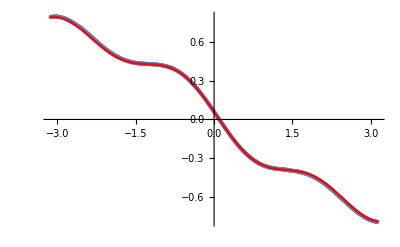

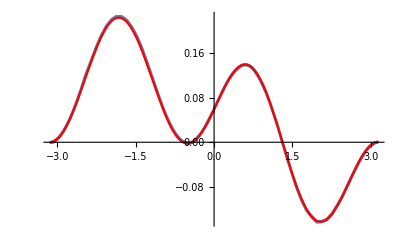

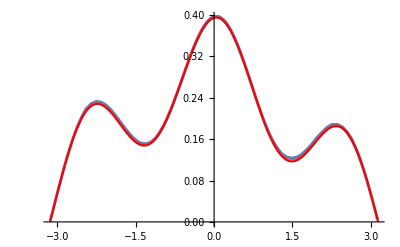

```mathematica
υ=0.99;
σ11N= {#,Sqrt[R0]/Knorm StressMatf[[1,1]]@@{υ R0 Cos[#],υ R0 Sin[#]}}&/@Range[-π+0.01,π-0.01,0.01];
σ22N= {#,Sqrt[R0]/Knorm StressMatf[[2,2]]@@{υ R0 Cos[#],υ R0 Sin[#]}}&/@Range[-π+0.01,π-0.01,0.01];
σ12N= {#,Sqrt[R0]/Knorm StressMatf[[1,2]]@@{υ R0 Cos[#],υ R0 Sin[#]}}&/@Range[-π+0.01,π-0.01,0.01];
Show[
ListPlot[σ11N],
Plot[σ11[θ],{θ,-π,π},PlotStyle->Red]]
Show[
ListPlot[σ22N],
Plot[σ22[θ],{θ,-π,π},PlotStyle->Red]]
Show[
ListPlot[σ12N],
Plot[σ12[θ],{θ,-π,π},PlotStyle->Red]]
```